## Omni Robot

In this note book the Vector tools by Dr. Alan A Barhorst was used. Please contact him via alan.barhorst@louisiana.edu for it. 
You can cite the work of this notebook using: 
Amarasiri, N., Barhorst, A.A. and Gottumukkala, R., 2022. Robust Dynamic Modeling and Trajectory Tracking Controller of a Universal Omni-Wheeled Mobile Robot. ASME Letters in Dynamic Systems and Control, 2(4), p.040902.
DOI: 10.1115/1.4055690

This paper can be downloaded using https://www.researchgate.net/profile/Nalaka-Amarasiri

Please cite the vector tools by using:
Barhorst, A. A., 1997, “Symbolic Equation Processing Utilizing Vector/Dyad Notation,” J. Sound Vib., 208(5), pp. 823–839.

## Please copy the Graphics, New Kinematic approach, Inverse Kinematics, and Dynamic Equations of Motion sells from Omni_robot_dynamics_PID_1.nb file on to this notebook to run the controller and simulation.

## Control Design

### Controller design

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
```

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

#### Control laws and control equations of motion

```mathematica
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
```

Here are the state equations for motor force and torque, desired minus actual is the error in a given state.  I will replace the place holder symbols for motor forces and torques with the states defined here later.

q_4-motor (1)

```mathematica
err[1]=Subscript[q, d4][t] -Subscript[q, 4][t];
eqM[1]=Subscript[Tm, 1]'[t]  - Subscript[K, Int][1]err[1] - Subscript[K, prop][1]D[err[1],t]- Subscript[K, deriv][1]D[err[1],{t,2}]
```

-K_Int[1] (-q_4[t]+q_d4[t])-K_prop[1] (-q_4'[t]+q_d4'[t])+Tm_1'[t]-K_deriv[1] (-q_4''[t]+q_d4''[t])

q_6-motor (2)

```mathematica
err[2]=Subscript[q, d6][t] - Subscript[q, 6][t];
eqM[2]=Subscript[Tm, 2]'[t] - Subscript[K, Int][2]err[2] - Subscript[K, prop][2]D[err[2],t]- Subscript[K, deriv][2]D[err[2],{t,2}]
```

-K_Int[2] (-q_6[t]+q_d6[t])-K_prop[2] (-q_6'[t]+q_d6'[t])+Tm_2'[t]-K_deriv[2] (-q_6''[t]+q_d6''[t])

q_8-motor (3)

```mathematica
err[3]=Subscript[q, d8][t] - Subscript[q, 8][t];
eqM[3]=Subscript[Tm, 3]'[t] - Subscript[K, Int][3]err[3] - Subscript[K, prop][3]D[err[3],t]- Subscript[K, deriv][3]D[err[3],{t,2}]
```

-K_Int[3] (-q_8[t]+q_d8[t])-K_prop[3] (-q_8'[t]+q_d8'[t])+Tm_3'[t]-K_deriv[3] (-q_8''[t]+q_d8''[t])

q_10-motor (4)

```mathematica
err[4]=Subscript[q, d10][t] - Subscript[q, 10][t];
eqM[4]=Subscript[Tm, 4]'[t] - Subscript[K, Int][4]err[4] - Subscript[K, prop][4]D[err[4],t]- Subscript[K, deriv][4]D[err[4],{t,2}]
```

-K_Int[4] (-q_10[t]+q_d10[t])-K_prop[4] (-q_10'[t]+q_d10'[t])+Tm_4'[t]-K_deriv[4] (-q_10''[t]+q_d10''[t])

Replace the place holders with the states for motor forces and torques.

```mathematica
eqC[1]=EQTT[1]//.{Subscript[T, mot][n_]-> Subscript[Tm, n][t],Subscript[ω, 1][t]-> Subscript[q, 4]'[t],Subscript[ω, 2][t]-> Subscript[q, 6]'[t],Subscript[ω, 3][t]-> Subscript[q, 8]'[t],Subscript[ω, 4][t]-> Subscript[q, 10]'[t],Subscript[ω, 1]'[t]-> Subscript[q, 4]''[t],Subscript[ω, 2]'[t]-> Subscript[q, 6]''[t],Subscript[ω, 3]'[t]-> Subscript[q, 8]''[t],Subscript[ω, 4]'[t]-> Subscript[q, 10]''[t]};
```

```mathematica
eqC[2]=EQTT[2]//.{Subscript[T, mot][n_]-> Subscript[Tm, n][t],Subscript[ω, 1][t]-> Subscript[q, 4]'[t],Subscript[ω, 2][t]-> Subscript[q, 6]'[t],Subscript[ω, 3][t]-> Subscript[q, 8]'[t],Subscript[ω, 4][t]-> Subscript[q, 10]'[t],Subscript[ω, 1]'[t]-> Subscript[q, 4]''[t],Subscript[ω, 2]'[t]-> Subscript[q, 6]''[t],Subscript[ω, 3]'[t]-> Subscript[q, 8]''[t],Subscript[ω, 4]'[t]-> Subscript[q, 10]''[t]};
```

```mathematica
eqC[3]=EQTT[3]//.{Subscript[T, mot][n_]-> Subscript[Tm, n][t],Subscript[ω, 1][t]-> Subscript[q, 4]'[t],Subscript[ω, 2][t]-> Subscript[q, 6]'[t],Subscript[ω, 3][t]-> Subscript[q, 8]'[t],Subscript[ω, 4][t]-> Subscript[q, 10]'[t],Subscript[ω, 1]'[t]-> Subscript[q, 4]''[t],Subscript[ω, 2]'[t]-> Subscript[q, 6]''[t],Subscript[ω, 3]'[t]-> Subscript[q, 8]''[t],Subscript[ω, 4]'[t]-> Subscript[q, 10]''[t]};
```

```mathematica
eqC[4]=EQTT[4]//.{Subscript[T, mot][n_]-> Subscript[Tm, n][t],Subscript[ω, 1][t]-> Subscript[q, 4]'[t],Subscript[ω, 2][t]-> Subscript[q, 6]'[t],Subscript[ω, 3][t]-> Subscript[q, 8]'[t],Subscript[ω, 4][t]-> Subscript[q, 10]'[t],Subscript[ω, 1]'[t]-> Subscript[q, 4]''[t],Subscript[ω, 2]'[t]-> Subscript[q, 6]''[t],Subscript[ω, 3]'[t]-> Subscript[q, 8]''[t],Subscript[ω, 4]'[t]-> Subscript[q, 10]''[t]};
```

Now we want to design the controller gains based on the step response of the system at a given motor.  We will do this by holding all the other states constant for the given motor control constant determination.  We will also linearize the system equations so we can then use pole placement techniques to size the gains.

#### Control gains q_4-motor (1)

q_4-motor. Here we fixate all the other movements.

```mathematica
eqG[1]=eqC[1]//.{Subscript[q, 1][t]-> 0,Subscript[q, 1]'[t]-> 0,Subscript[q, 1]''[t]-> 0,Subscript[q, 2][t]-> 0,Subscript[q, 2]'[t]-> 0,Subscript[q, 2]''[t]-> 0,Subscript[q, 3][t]-> 0,Subscript[q, 3]'[t]-> 0,Subscript[q, 3]''[t]-> 0,(*Subscript[q, 4][t]-> 0,Subscript[q, 4]'[t]-> 0,Subscript[q, 4]''[t]-> 0,*)Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0,Subscript[q, 11][t]-> 0,Subscript[q, 11]'[t]-> 0,Subscript[q, 11]''[t]-> 0}//.{(*Subscript[Tm, 1][t]->0,*)Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{r-> 0.4,R-> 3}//Chop
```

Tm_1[t]-0.00123292 Cos[q_4[t]] Sin[q_4[t]] q_4'[t]^2+1.5 (-0.0023118 q_4'[t]^2-0.0271251 q_4''[t])+1.5 (0.0023118 q_4'[t]^2-0.0271251 q_4''[t])+1.5 (-0.00175104 q_4'[t]^2-0.0205456 q_4''[t])+1.5 (0.00175104 q_4'[t]^2-0.0205456 q_4''[t])+0.75 (0.0046236 q_4'[t]^2-0.0135625 q_4''[t])+0.75 (0.00350208 q_4'[t]^2-0.0102728 q_4''[t])+1.5 (-0.000128625 q_4'[t]^2-0.0015092 q_4''[t])+1.5 (0.000128625 q_4'[t]^2-0.0015092 q_4''[t])+0.75 (0.000257249 q_4'[t]^2-0.000754598 q_4''[t])-0.75 (0.000257249 q_4'[t]^2+0.000754598 q_4''[t])-0.75 (0.00350208 q_4'[t]^2+0.0102728 q_4''[t])-0.75 (0.0046236 q_4'[t]^2+0.0135625 q_4''[t])-0.593888 q_4''[t]-0.170455 (0.-0.0000378041 Cos[q_4[t]] Sin[q_4[t]] q_4'[t]^2+0.0000378041 Cos[q_4[t]]^2 q_4''[t]+0.0000189021 Sin[q_4[t]]^2 q_4''[t])-0.170455 (-0.0144284 Cos[q_4[t]] Sin[q_4[t]] q_4'[t]^2+0.0148814 Cos[q_4[t]]^2 q_4''[t]+0.00766719 Sin[q_4[t]]^2 q_4''[t])-0.170455 (0.0133196 Cos[q_4[t]]^2 q_4''[t]+0.0133196 Sin[q_4[t]]^2 q_4''[t])

Linearize the equation.

```mathematica
eqL[1]=Normal[Series[eqG[1],{Subscript[q, 4][t],0,1},{Subscript[q, 4]'[t],0,1}]](*The simplest solution to this is to linearize the equation of motion around a desired operating point,then apply traditional linear controls methods.The validity of this approach is restricted to small motions about the operating point. Link http://web.mit.edu/2.737/www/MagLev/linearized/*)
```

Tm_1[t]-0.783125 q_4''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[1]=D[eqL[1],t]
```

Tm_1'[t]-0.783125 q_4^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[1]=Solve[eqM[1]==0,Subscript[Tm, 1]'[t]]//First
```

{Tm_1'[t]→-K_Int[1] q_4[t]+K_Int[1] q_d4[t]-K_prop[1] q_4'[t]+K_prop[1] q_d4'[t]-K_deriv[1] q_4''[t]+K_deriv[1] q_d4''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[1]=eqLd[1]//.solM[1]
```

-K_Int[1] q_4[t]+K_Int[1] q_d4[t]-K_prop[1] q_4'[t]+K_prop[1] q_d4'[t]-K_deriv[1] q_4''[t]+K_deriv[1] q_d4''[t]-0.783125 q_4^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[1]=eqLf[1]//.{Derivative[n_][Subscript[q, 4]][t]->s^n,Subscript[q, 4][t]->1,Subscript[q, d4][t]->0,Subscript[q, d4]'[t]->0,Subscript[q, d4]''[t]->0}
```

-0.783125 s^3-s^2 K_deriv[1]-K_Int[1]-s K_prop[1]

Put the characteristic equation in standard form.

```mathematica
charEq[1]=charEq[1]/Coefficient[charEq[1],s^3]//Expand
```

1. s^3+1.27693 s^2 K_deriv[1]+1.27693 K_Int[1]+1.27693 s K_prop[1]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[1]=Expand[(s+Subscript[a, 1])(s^2+ 2 Subscript[ζ, 1] Subscript[ω, n1] s + Subscript[ω, n1]^2)]
```

s^3+s^2 a_1+2 s^2 ζ_1 ω_n1+2 s a_1 ζ_1 ω_n1+s ω_n1^2+a_1 ω_n1^2

The time to peak is defined as

```mathematica
eqTp[1]=Subscript[t, p1]== π/(Subscript[ω, n1] √(1-Subscript[ζ, 1]^2));
```

The two percent settling time is given by

```mathematica
eqTs[1]=Subscript[t, s1]== 4/(Subscript[ζ, 1] Subscript[ω, n1]);
```

```mathematica
solZW[1]=Solve[{eqTp[1],eqTs[1]},{Subscript[ζ, 1],Subscript[ω, n1]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_1→(4 t_p1)/(√(16 t_p1^2+π^2 t_s1^2)),ω_n1→(√(16 t_p1^2+π^2 t_s1^2))/(t_p1 t_s1)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[1]=Coefficient[charEq[1],s^2]==Coefficient[charDesired[1],s^2]/.solZW[1]
```

1.27693 K_deriv[1]==a_1+8/t_s1

```mathematica
eqGain2[1]=Coefficient[charEq[1],s]==Coefficient[charDesired[1],s]/.solZW[1]
```

1.27693 K_prop[1]==(8 a_1)/t_s1+(16 t_p1^2+π^2 t_s1^2)/(t_p1^2 t_s1^2)

```mathematica
eqGain3[1]=(charEq[1]/.s->0)==(charDesired[1]/.s->0)/.solZW[1]
```

0.+1.27693 K_Int[1]==(a_1 (16 t_p1^2+π^2 t_s1^2))/(t_p1^2 t_s1^2)

Solve for the controller gains.

```mathematica
solGains[1]=Solve[{eqGain1[1],eqGain2[1],eqGain3[1]},{Subscript[K, prop][1],Subscript[K, Int][1],Subscript[K, deriv][1]}]//First
```

{K_prop[1]→0.783125 ((8. a_1)/t_s1+(1. (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_Int[1]→0.783125 (0.+(1. a_1 (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_deriv[1]→0.783125 (1. a_1+8./t_s1)}

Now set the time constants.

```mathematica
tConstRules[1]={Subscript[a, 1]->100,Subscript[t, p1]->1/4,Subscript[t, s1]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[q, d4][t_]:=stepMag UnitStep[t]
stepSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,Subscript[q, 4]'[Subscript[t, 0]]==0,Subscript[q, 4][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 4],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_4→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

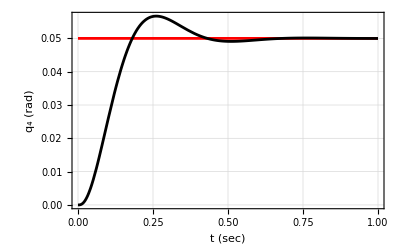

```mathematica
Plot[{Subscript[q, d4][t],Subscript[q, 4][t]/.stepSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_4 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

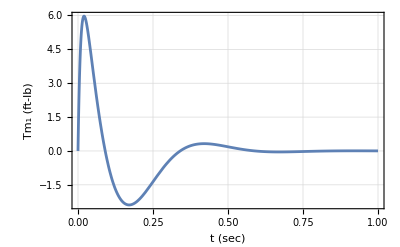

```mathematica
Plot[Subscript[Tm, 1][t]/.stepSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (ft-lb)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 0.4 lb-ft peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d4][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,Subscript[q, 4]'[Subscript[t, 0]]==0,Subscript[q, 4][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 4],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_4→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

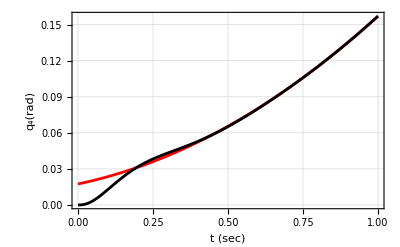

```mathematica
Plot[{Subscript[q, d4][t],Subscript[q, 4][t]/.trackSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_4(rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

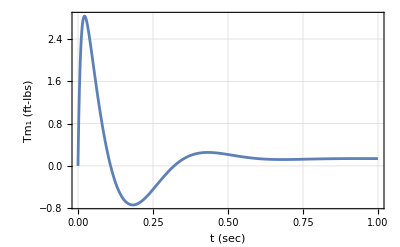

```mathematica
Plot[Subscript[Tm, 1][t]/.trackSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (ft-lbs)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d4][t_]=.
```

#### Control gains q_6-motor (2)

q_6-motor. Here we fixate all the other movements.

```mathematica
eqG[2]=eqC[2]//.{Subscript[q, 1][t]-> 0,Subscript[q, 1]'[t]-> 0,Subscript[q, 1]''[t]-> 0,Subscript[q, 2][t]-> 0,Subscript[q, 2]'[t]-> 0,Subscript[q, 2]''[t]-> 0,Subscript[q, 3][t]-> 0,Subscript[q, 3]'[t]-> 0,Subscript[q, 3]''[t]-> 0,Subscript[q, 4][t]-> 0,Subscript[q, 4]'[t]-> 0,Subscript[q, 4]''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0(*,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0*),Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0,Subscript[q, 11][t]-> 0,Subscript[q, 11]'[t]-> 0,Subscript[q, 11]''[t]-> 0}//.{Subscript[Tm, 1][t]->0,(*Subscript[Tm, 2][t]->0,*)Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{r-> 0.4,R-> 3}//Chop
```

Tm_2[t]-0.00118794 Cos[q_6[t]] Sin[q_6[t]] q_6'[t]^2+1.5 (-0.0023118 q_6'[t]^2-0.0271251 q_6''[t])+1.5 (0.0023118 q_6'[t]^2-0.0271251 q_6''[t])+1.5 (-0.00175104 q_6'[t]^2-0.0205456 q_6''[t])+1.5 (0.00175104 q_6'[t]^2-0.0205456 q_6''[t])+0.75 (-0.0046236 q_6'[t]^2-0.0135625 q_6''[t])+0.75 (-0.00350208 q_6'[t]^2-0.0102728 q_6''[t])+1.5 (-0.000128625 q_6'[t]^2-0.0015092 q_6''[t])+1.5 (0.000128625 q_6'[t]^2-0.0015092 q_6''[t])+0.75 (-0.000257249 q_6'[t]^2-0.000754598 q_6''[t])-0.75 (-0.000257249 q_6'[t]^2+0.000754598 q_6''[t])-0.75 (-0.00350208 q_6'[t]^2+0.0102728 q_6''[t])-0.75 (-0.0046236 q_6'[t]^2+0.0135625 q_6''[t])-0.592429 q_6''[t]+0.170455 (-0.0133196 Cos[q_6[t]]^2 q_6''[t]-0.0133196 Sin[q_6[t]]^2 q_6''[t])+0.170455 (0.0139006 Cos[q_6[t]] Sin[q_6[t]] q_6'[t]^2-0.0143536 Cos[q_6[t]]^2 q_6''[t]-0.0074033 Sin[q_6[t]]^2 q_6''[t])+0.170455 (0.0000378041 Cos[q_6[t]] Sin[q_6[t]] q_6'[t]^2-0.0000378041 Cos[q_6[t]]^2 q_6''[t]-0.0000189021 Sin[q_6[t]]^2 q_6''[t])

Linearize the equation.

```mathematica
eqL[2]=Normal[Series[eqG[2],{Subscript[q, 6][t],0,1},{Subscript[q, 6]'[t],0,1}]]
```

Tm_2[t]-0.781577 q_6''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[2]=D[eqL[2],t]
```

Tm_2'[t]-0.781577 q_6^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[2]=Solve[eqM[2]==0,Subscript[Tm, 2]'[t]]//First
```

{Tm_2'[t]→-K_Int[2] q_6[t]+K_Int[2] q_d6[t]-K_prop[2] q_6'[t]+K_prop[2] q_d6'[t]-K_deriv[2] q_6''[t]+K_deriv[2] q_d6''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[2]=eqLd[2]//.solM[2]
```

-K_Int[2] q_6[t]+K_Int[2] q_d6[t]-K_prop[2] q_6'[t]+K_prop[2] q_d6'[t]-K_deriv[2] q_6''[t]+K_deriv[2] q_d6''[t]-0.781577 q_6^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[2]=eqLf[2]//.{Derivative[n_][Subscript[q, 6]][t]->s^n,Subscript[q, 6][t]->1,Subscript[q, d6][t]->0,Subscript[q, d6]'[t]->0,Subscript[q, d6]''[t]->0}
```

-0.781577 s^3-s^2 K_deriv[2]-K_Int[2]-s K_prop[2]

Put the characteristic equation in standard form.

```mathematica
charEq[2]=charEq[2]/Coefficient[charEq[2],s^3]//Expand
```

1. s^3+1.27946 s^2 K_deriv[2]+1.27946 K_Int[2]+1.27946 s K_prop[2]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[2]=Expand[(s+Subscript[a, 2])(s^2+ 2 Subscript[ζ, 2] Subscript[ω, n2] s + Subscript[ω, n2]^2)]
```

s^3+s^2 a_2+2 s^2 ζ_2 ω_n2+2 s a_2 ζ_2 ω_n2+s ω_n2^2+a_2 ω_n2^2

The time to peak is defined as

```mathematica
eqTp[2]=Subscript[t, p2]== π/(Subscript[ω, n2] √(1-Subscript[ζ, 2]^2));
```

The two percent settling time is given by

```mathematica
eqTs[2]=Subscript[t, s2]== 4/(Subscript[ζ, 2] Subscript[ω, n2]);
```

```mathematica
solZW[2]=Solve[{eqTp[2],eqTs[2]},{Subscript[ζ, 2],Subscript[ω, n2]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_2→(4 t_p2)/(√(16 t_p2^2+π^2 t_s2^2)),ω_n2→(√(16 t_p2^2+π^2 t_s2^2))/(t_p2 t_s2)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[2]=Coefficient[charEq[2],s^2]==Coefficient[charDesired[2],s^2]/.solZW[2]
```

1.27946 K_deriv[2]==a_2+8/t_s2

```mathematica
eqGain2[2]=Coefficient[charEq[2],s]==Coefficient[charDesired[2],s]/.solZW[2]
```

1.27946 K_prop[2]==(8 a_2)/t_s2+(16 t_p2^2+π^2 t_s2^2)/(t_p2^2 t_s2^2)

```mathematica
eqGain3[2]=(charEq[2]/.s->0)==(charDesired[2]/.s->0)/.solZW[2]
```

0.+1.27946 K_Int[2]==(a_2 (16 t_p2^2+π^2 t_s2^2))/(t_p2^2 t_s2^2)

Solve for the controller gains.

```mathematica
solGains[2]=Solve[{eqGain1[2],eqGain2[2],eqGain3[2]},{Subscript[K, prop][2],Subscript[K, Int][2],Subscript[K, deriv][2]}]//First
```

{K_prop[2]→0.781577 ((8. a_2)/t_s2+(1. (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_Int[2]→0.781577 (0.+(1. a_2 (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_deriv[2]→0.781577 (1. a_2+8./t_s2)}

Now set the time constants.

```mathematica
tConstRules[2]={Subscript[a, 2]->100,Subscript[t, p2]->1/4,Subscript[t, s2]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[q, d6][t_]:=stepMag UnitStep[t]
stepSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

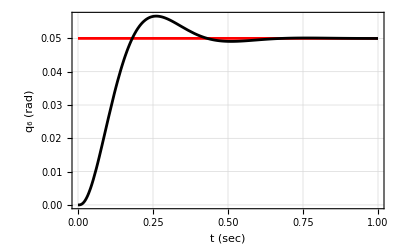

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.stepSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

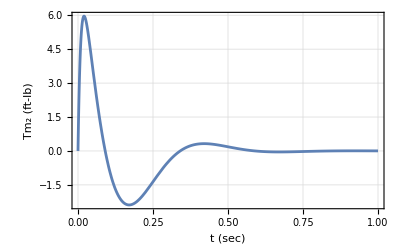

```mathematica
Plot[Subscript[Tm, 2][t]/.stepSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (ft-lb)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 0.4 lb-ft peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d6][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

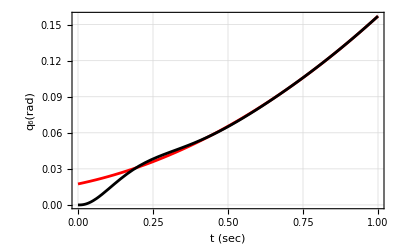

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.trackSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6(rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

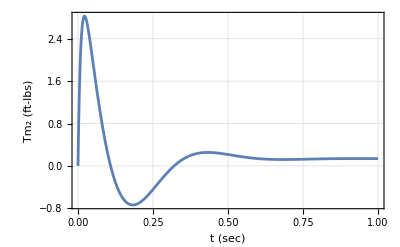

```mathematica
Plot[Subscript[Tm, 2][t]/.trackSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (ft-lbs)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d6][t_]=.
```

#### Control gains q_8-motor (3)

q_8-motor. Here we fixate all the other movements.

```mathematica
eqG[3]=eqC[3]//.{Subscript[q, 1][t]-> 0,Subscript[q, 1]'[t]-> 0,Subscript[q, 1]''[t]-> 0,Subscript[q, 2][t]-> 0,Subscript[q, 2]'[t]-> 0,Subscript[q, 2]''[t]-> 0,Subscript[q, 3][t]-> 0,Subscript[q, 3]'[t]-> 0,Subscript[q, 3]''[t]-> 0,Subscript[q, 4][t]-> 0,Subscript[q, 4]'[t]-> 0,Subscript[q, 4]''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,(*Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,*)Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0,Subscript[q, 11][t]-> 0,Subscript[q, 11]'[t]-> 0,Subscript[q, 11]''[t]-> 0}//.{Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,(*Subscript[Tm, 3][t]->0,*)Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{r-> 0.4,R-> 3}//Chop
```

Tm_3[t]-3.22194×10^-6 Cos[q_8[t]] Sin[q_8[t]] q_8'[t]^2+0.75 (0.0046236 q_8'[t]^2-0.0135625 q_8''[t])+0.75 (0.00350208 q_8'[t]^2-0.0102728 q_8''[t])+0.75 (0.000257249 q_8'[t]^2-0.000754598 q_8''[t])-0.75 (0.000257249 q_8'[t]^2+0.000754598 q_8''[t])-1.5 (-0.000128625 q_8'[t]^2+0.0015092 q_8''[t])-1.5 (0.000128625 q_8'[t]^2+0.0015092 q_8''[t])-0.75 (0.00350208 q_8'[t]^2+0.0102728 q_8''[t])-0.75 (0.0046236 q_8'[t]^2+0.0135625 q_8''[t])-1.5 (-0.00175104 q_8'[t]^2+0.0205456 q_8''[t])-1.5 (0.00175104 q_8'[t]^2+0.0205456 q_8''[t])-1.5 (-0.0023118 q_8'[t]^2+0.0271251 q_8''[t])-1.5 (0.0023118 q_8'[t]^2+0.0271251 q_8''[t])-0.634389 q_8''[t]-0.170455 (-0.0000378041 Cos[q_8[t]] Sin[q_8[t]] q_8'[t]^2+0.0000378041 Cos[q_8[t]]^2 q_8''[t]+0.0000189021 Sin[q_8[t]]^2 q_8''[t])-0.170455 (0.0074033 Cos[q_8[t]]^2 q_8''[t]+0.0074033 Sin[q_8[t]]^2 q_8''[t])-0.170455 (0.0133196 Cos[q_8[t]]^2 q_8''[t]+0.0133196 Sin[q_8[t]]^2 q_8''[t])

Linearize the equation.

```mathematica
eqL[3]=Normal[Series[eqG[3],{Subscript[q, 8][t],0,1},{Subscript[q, 8]'[t],0,1}]]
```

Tm_3[t]-0.822353 q_8''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[3]=D[eqL[3],t]
```

Tm_3'[t]-0.822353 q_8^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[3]=Solve[eqM[3]==0,Subscript[Tm, 3]'[t]]//First
```

{Tm_3'[t]→-K_Int[3] q_8[t]+K_Int[3] q_d8[t]-K_prop[3] q_8'[t]+K_prop[3] q_d8'[t]-K_deriv[3] q_8''[t]+K_deriv[3] q_d8''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[3]=eqLd[3]//.solM[3]
```

-K_Int[3] q_8[t]+K_Int[3] q_d8[t]-K_prop[3] q_8'[t]+K_prop[3] q_d8'[t]-K_deriv[3] q_8''[t]+K_deriv[3] q_d8''[t]-0.822353 q_8^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[3]=eqLf[3]//.{Derivative[n_][Subscript[q, 8]][t]->s^n,Subscript[q, 8][t]->1,Subscript[q, d8][t]->0,Subscript[q, d8]'[t]->0,Subscript[q, d8]''[t]->0}
```

-0.822353 s^3-s^2 K_deriv[3]-K_Int[3]-s K_prop[3]

Put the characteristic equation in standard form.

```mathematica
charEq[3]=charEq[3]/Coefficient[charEq[3],s^3]//Expand
```

1. s^3+1.21602 s^2 K_deriv[3]+1.21602 K_Int[3]+1.21602 s K_prop[3]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[3]=Expand[(s+Subscript[a, 3])(s^2+ 2 Subscript[ζ, 3] Subscript[ω, n3] s + Subscript[ω, n3]^2)]
```

s^3+s^2 a_3+2 s^2 ζ_3 ω_n3+2 s a_3 ζ_3 ω_n3+s ω_n3^2+a_3 ω_n3^2

The time to peak is defined as

```mathematica
eqTp[3]=Subscript[t, p3]== π/(Subscript[ω, n3] √(1-Subscript[ζ, 3]^2));
```

The two percent settling time is given by

```mathematica
eqTs[3]=Subscript[t, s3]== 4/(Subscript[ζ, 3] Subscript[ω, n3]);
```

```mathematica
solZW[3]=Solve[{eqTp[3],eqTs[3]},{Subscript[ζ, 3],Subscript[ω, n3]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_3→(4 t_p3)/(√(16 t_p3^2+π^2 t_s3^2)),ω_n3→(√(16 t_p3^2+π^2 t_s3^2))/(t_p3 t_s3)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[3]=Coefficient[charEq[3],s^2]==Coefficient[charDesired[3],s^2]/.solZW[3]
```

1.21602 K_deriv[3]==a_3+8/t_s3

```mathematica
eqGain2[3]=Coefficient[charEq[3],s]==Coefficient[charDesired[3],s]/.solZW[3]
```

1.21602 K_prop[3]==(8 a_3)/t_s3+(16 t_p3^2+π^2 t_s3^2)/(t_p3^2 t_s3^2)

```mathematica
eqGain3[3]=(charEq[3]/.s->0)==(charDesired[3]/.s->0)/.solZW[3]
```

0.+1.21602 K_Int[3]==(a_3 (16 t_p3^2+π^2 t_s3^2))/(t_p3^2 t_s3^2)

Solve for the controller gains.

```mathematica
solGains[3]=Solve[{eqGain1[3],eqGain2[3],eqGain3[3]},{Subscript[K, prop][3],Subscript[K, Int][3],Subscript[K, deriv][3]}]//First
```

{K_prop[3]→0.822353 ((8. a_3)/t_s3+(1. (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_Int[3]→0.822353 (0.+(1. a_3 (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_deriv[3]→0.822353 (1. a_3+8./t_s3)}

Now set the time constants.

```mathematica
tConstRules[3]={Subscript[a, 3]->100,Subscript[t, p3]->1/4,Subscript[t, s3]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[q, d8][t_]:=stepMag UnitStep[t]
stepSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 8]'[Subscript[t, 0]]==0,Subscript[q, 8][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 8],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_8→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

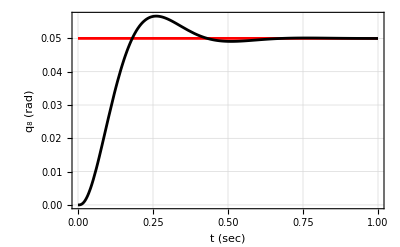

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.stepSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

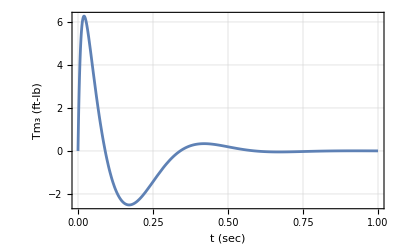

```mathematica
Plot[Subscript[Tm, 3][t]/.stepSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (ft-lb)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 0.4 lb-ft peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d8][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 8]'[Subscript[t, 0]]==0,Subscript[q, 8][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 8],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_8→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

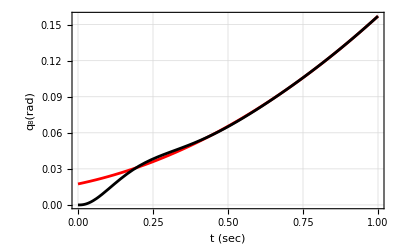

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.trackSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8(rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

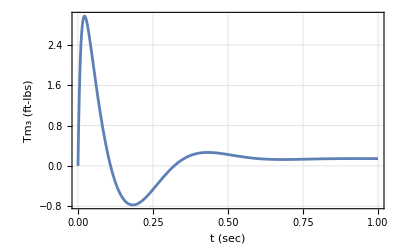

```mathematica
Plot[Subscript[Tm, 3][t]/.trackSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (ft-lbs)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d8][t_]=.
```

#### Control gains q_10-motor (4)

q_10-motor. Here we fixate all the other movements.

```mathematica
eqG[4]=eqC[4]//.{Subscript[q, 1][t]-> 0,Subscript[q, 1]'[t]-> 0,Subscript[q, 1]''[t]-> 0,Subscript[q, 2][t]-> 0,Subscript[q, 2]'[t]-> 0,Subscript[q, 2]''[t]-> 0,Subscript[q, 3][t]-> 0,Subscript[q, 3]'[t]-> 0,Subscript[q, 3]''[t]-> 0,Subscript[q, 4][t]-> 0,Subscript[q, 4]'[t]-> 0,Subscript[q, 4]''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,(*Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0,*)Subscript[q, 11][t]-> 0,Subscript[q, 11]'[t]-> 0,Subscript[q, 11]''[t]-> 0}//.{Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,(*Subscript[Tm, 4][t]->0,*)Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{r-> 0.4,R-> 3}//Chop
```

Tm_4[t]-3.22194×10^-6 Cos[q_10[t]] Sin[q_10[t]] q_10'[t]^2+0.75 (-0.0046236 q_10'[t]^2-0.0135625 q_10''[t])+0.75 (-0.00350208 q_10'[t]^2-0.0102728 q_10''[t])+0.75 (-0.000257249 q_10'[t]^2-0.000754598 q_10''[t])-0.75 (-0.000257249 q_10'[t]^2+0.000754598 q_10''[t])-1.5 (-0.000128625 q_10'[t]^2+0.0015092 q_10''[t])-1.5 (0.000128625 q_10'[t]^2+0.0015092 q_10''[t])-0.75 (-0.00350208 q_10'[t]^2+0.0102728 q_10''[t])-0.75 (-0.0046236 q_10'[t]^2+0.0135625 q_10''[t])-1.5 (-0.00175104 q_10'[t]^2+0.0205456 q_10''[t])-1.5 (0.00175104 q_10'[t]^2+0.0205456 q_10''[t])-1.5 (-0.0023118 q_10'[t]^2+0.0271251 q_10''[t])-1.5 (0.0023118 q_10'[t]^2+0.0271251 q_10''[t])-0.634389 q_10''[t]+0.170455 (-0.0133196 Cos[q_10[t]]^2 q_10''[t]-0.0133196 Sin[q_10[t]]^2 q_10''[t])+0.170455 (-0.0074033 Cos[q_10[t]]^2 q_10''[t]-0.0074033 Sin[q_10[t]]^2 q_10''[t])+0.170455 (0.0000378041 Cos[q_10[t]] Sin[q_10[t]] q_10'[t]^2-0.0000378041 Cos[q_10[t]]^2 q_10''[t]-0.0000189021 Sin[q_10[t]]^2 q_10''[t])

Linearize the equation.

```mathematica
eqL[4]=Normal[Series[eqG[4],{Subscript[q, 10][t],0,1},{Subscript[q, 10]'[t],0,1}]]
```

Tm_4[t]-0.822353 q_10''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[4]=D[eqL[4],t]
```

Tm_4'[t]-0.822353 q_10^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[4]=Solve[eqM[4]==0,Subscript[Tm, 4]'[t]]//First
```

{Tm_4'[t]→-K_Int[4] q_10[t]+K_Int[4] q_d10[t]-K_prop[4] q_10'[t]+K_prop[4] q_d10'[t]-K_deriv[4] q_10''[t]+K_deriv[4] q_d10''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[4]=eqLd[4]//.solM[4]
```

-K_Int[4] q_10[t]+K_Int[4] q_d10[t]-K_prop[4] q_10'[t]+K_prop[4] q_d10'[t]-K_deriv[4] q_10''[t]+K_deriv[4] q_d10''[t]-0.822353 q_10^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[4]=eqLf[4]//.{Derivative[n_][Subscript[q, 10]][t]->s^n,Subscript[q, 10][t]->1,Subscript[q, d10][t]->0,Subscript[q, d10]'[t]->0,Subscript[q, d10]''[t]->0}
```

-0.822353 s^3-s^2 K_deriv[4]-K_Int[4]-s K_prop[4]

Put the characteristic equation in standard form.

```mathematica
charEq[4]=charEq[4]/Coefficient[charEq[4],s^3]//Expand
```

1. s^3+1.21602 s^2 K_deriv[4]+1.21602 K_Int[4]+1.21602 s K_prop[4]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[4]=Expand[(s+Subscript[a, 4])(s^2+ 2 Subscript[ζ, 4] Subscript[ω, n4] s + Subscript[ω, n4]^2)]
```

s^3+s^2 a_4+2 s^2 ζ_4 ω_n4+2 s a_4 ζ_4 ω_n4+s ω_n4^2+a_4 ω_n4^2

The time to peak is defined as

```mathematica
eqTp[4]=Subscript[t, p4]== π/(Subscript[ω, n4] √(1-Subscript[ζ, 4]^2));
```

The two percent settling time is given by

```mathematica
eqTs[4]=Subscript[t, s4]== 4/(Subscript[ζ, 4] Subscript[ω, n4]);
```

```mathematica
solZW[4]=Solve[{eqTp[4],eqTs[4]},{Subscript[ζ, 4],Subscript[ω, n4]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_4→(4 t_p4)/(√(16 t_p4^2+π^2 t_s4^2)),ω_n4→(√(16 t_p4^2+π^2 t_s4^2))/(t_p4 t_s4)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[4]=Coefficient[charEq[4],s^2]==Coefficient[charDesired[4],s^2]/.solZW[4]
```

1.21602 K_deriv[4]==a_4+8/t_s4

```mathematica
eqGain2[4]=Coefficient[charEq[4],s]==Coefficient[charDesired[4],s]/.solZW[4]
```

1.21602 K_prop[4]==(8 a_4)/t_s4+(16 t_p4^2+π^2 t_s4^2)/(t_p4^2 t_s4^2)

```mathematica
eqGain3[4]=(charEq[4]/.s->0)==(charDesired[4]/.s->0)/.solZW[4]
```

0.+1.21602 K_Int[4]==(a_4 (16 t_p4^2+π^2 t_s4^2))/(t_p4^2 t_s4^2)

Solve for the controller gains.

```mathematica
solGains[4]=Solve[{eqGain1[4],eqGain2[4],eqGain3[4]},{Subscript[K, prop][4],Subscript[K, Int][4],Subscript[K, deriv][4]}]//First
```

{K_prop[4]→0.822353 ((8. a_4)/t_s4+(1. (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_Int[4]→0.822353 (0.+(1. a_4 (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_deriv[4]→0.822353 (1. a_4+8./t_s4)}

Now set the time constants.

```mathematica
tConstRules[4]={Subscript[a, 4]->100,Subscript[t, p4]->1/4,Subscript[t, s4]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[q, d10][t_]:=stepMag UnitStep[t]
stepSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 10]'[Subscript[t, 0]]==0,Subscript[q, 10][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 10],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_10→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

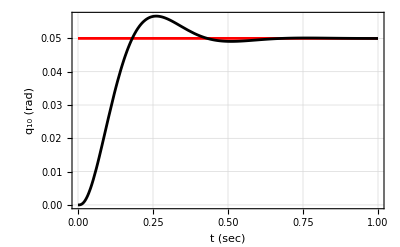

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.stepSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

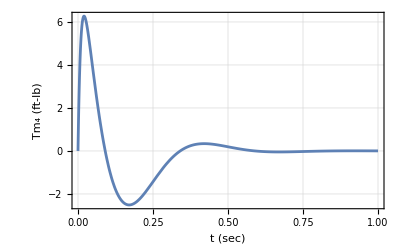

```mathematica
Plot[Subscript[Tm, 4][t]/.stepSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (ft-lb)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 0.4 lb-ft peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d10][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 10]'[Subscript[t, 0]]==0,Subscript[q, 10][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 10],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_10→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

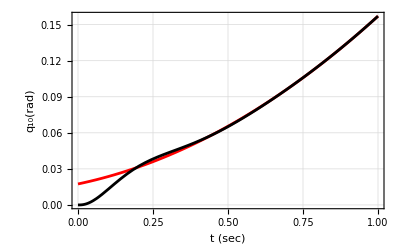

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.trackSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10(rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

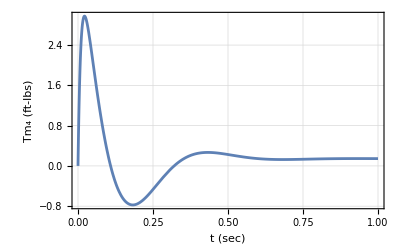

```mathematica
Plot[Subscript[Tm, 4][t]/.trackSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (ft-lbs)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d10][t_]=.
```

## Path planning

In this section we will generate a path we want the robot to follow.  We will then pass this information to the robot via desired position and angle coordinates.  Mathematica's interpolation function can be set up where a given interpolation is fit with a sufficiently smooth spline through the desired points.  Each data set for the desired path will consist of a space point and orientation.

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

Unset::norep: Assignment on Subscript for q_5[t_] not found.

Unset::norep: Assignment on Subscript for q_6[t_] not found.

Unset::norep: Assignment on Subscript for q_7[t_] not found.

Unset::norep: Assignment on Subscript for q_8[t_] not found.

Unset::norep: Assignment on Subscript for q_9[t_] not found.

Unset::norep: Assignment on Subscript for q_10[t_] not found.

Unset::norep: Assignment on Subscript for q_11[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

Unset::norep: Assignment on Subscript for T_mot[1] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[2] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[3] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[4] not found.

$Failed

-Graphics3D-

#### Path Function

Let the path define in terms of geometry as following.

```mathematica
Subscript[T, man]=10;(*Total manuaring time*)
delT = 0.25;(*Time steps*)
```

```mathematica
A=20;B=20;Cc=0;ω=2 Pi (1/Subscript[T, man]);
```

Path trace in space. Here note that the robot is moving only on the x-y plane. Therefore Z plane function is Zero. And also note that the Z (q_z[t])and q_3[t] are NOT the same.

```mathematica
Subscript[q, d1][t_]:= A(1- Sin[2ω t])
Subscript[q, d2][t_]:=A(1- Sin[ω t])
Subscript[q, d3][t_]:=π/4
Subscript[q, z][t_]:=0
```

Let’s take the derivative of the above q_p1[t], q_p2[t] , q_p3[t]

```mathematica
Subscript[q, d1]'[t]
Subscript[q, d2]'[t]
Subscript[q, d3]'[t]
Subscript[q, z]'[t]
```

-8 π Cos[(2 π t)/5]

-4 π Cos[(π t)/5]

0

0

```mathematica
rot3[Subscript[q, d3][t]]
```

{{1/(√2),1/(√2),0},{-1/(√2),1/(√2),0},{0,0,1}}

```mathematica
scale=40;
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,scale},{-0.5scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]
```

-Graphics3D-

```mathematica
scale=40;
pathvelocityPlot=ParametricPlot3D[{Subscript[q, d1]'[t],Subscript[q, d2]'[t],Subscript[q, d3]'[t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,scale},{-0.5scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]
```

-Graphics3D-

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

Unset::norep: Assignment on Subscript for q_5[t_] not found.

Unset::norep: Assignment on Subscript for q_6[t_] not found.

Unset::norep: Assignment on Subscript for q_7[t_] not found.

Unset::norep: Assignment on Subscript for q_8[t_] not found.

Unset::norep: Assignment on Subscript for q_9[t_] not found.

Unset::norep: Assignment on Subscript for q_10[t_] not found.

Unset::norep: Assignment on Subscript for q_11[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for (π/5)_1[t_] not found.

Unset::norep: Assignment on Subscript for (π/5)_2[t_] not found.

Unset::norep: Assignment on Subscript for (π/5)_3[t_] not found.

Unset::norep: Assignment on Subscript for (π/5)_4[t_] not found.

Unset::norep: Assignment on Subscript for T_mot[1] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[2] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[3] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[4] not found.

$Failed

-Graphics3D-

#### FKE for the robot

```mathematica
(*eqk1=Subscript[q, 1]'[t]==B1;
eqk2=Subscript[q, 2]'[t]==B2;
eqOmega=Subscript[q, 3]'[t]==B3;*)
A=20;B=20;Cc=0;ω=2 Pi (1/Subscript[T, man]);R=3;r=0.4;
Subscript[q, d1][t_]= A(1- Sin[2ω t]);
Subscript[q, d2][t_]=A(1- Sin[ω t]);
Subscript[q, d3][t_]=t;
Subscript[q, z][t_]=0;
Subscript[q, d1]'[t];
Subscript[q, d2]'[t];
Subscript[q, d3]'[t];
Subscript[q, d1]''[t];
Subscript[q, d2]''[t];
Subscript[q, d3]''[t];
Subscript[q, d4]'[t_]=(1. Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R+(1. Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R-(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d6]'[t_]=(1. Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R+(1. Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R+(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d8]'[t_]=(1. Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R-(1. Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R-(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d10]'[t_]=(1. Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t])/R-(1. Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/R+(4.4 Subscript[q, 3]'[t])/R//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d5]'[t_]=(Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t]-Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d7]'[t_]=(Sin[Subscript[q, 3][t]] Subscript[q, 1]'[t]-Cos[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d9]'[t_]=(Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t]+Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
Subscript[q, d11]'[t_]=(Cos[Subscript[q, 3][t]] Subscript[q, 1]'[t]+Sin[Subscript[q, 3][t]] Subscript[q, 2]'[t])/r//.{Subscript[q, 1][t]-> Subscript[q, d1][t],Subscript[q, 2][t]-> Subscript[q, d2][t],Subscript[q, 3][t]-> Subscript[q, d3][t],Subscript[q, 1]'[t]-> Subscript[q, d1]'[t],Subscript[q, 2]'[t]-> Subscript[q, d2]'[t],Subscript[q, 3]'[t]-> Subscript[q, d3]'[t]};
```

#### q_1 desired

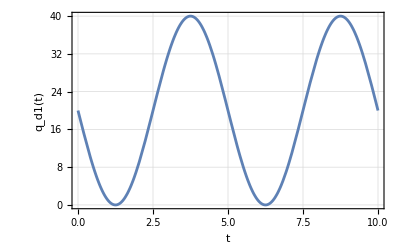

```mathematica
Plot[Subscript[q, d1][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d1(t)"},Frame->True,GridLines-> Automatic]
```

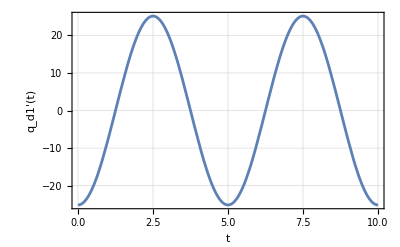

```mathematica
Plot[Subscript[q, d1]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d1'(t)"},Frame->True,GridLines-> Automatic]
```

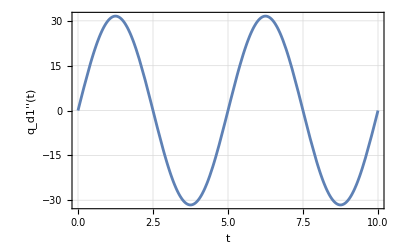

```mathematica
Plot[Subscript[q, d1]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d1''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_2 desired

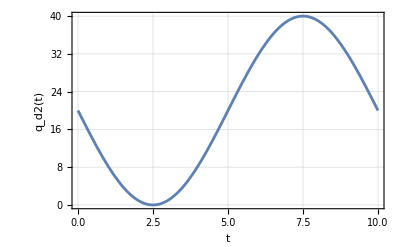

```mathematica
Plot[Subscript[q, d2][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d2(t)"},Frame->True,GridLines-> Automatic]
```

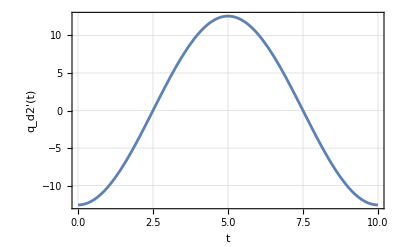

```mathematica
Plot[Subscript[q, d2]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d2'(t)"},Frame->True,GridLines-> Automatic]
```

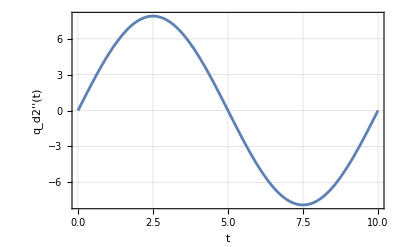

```mathematica
Plot[Subscript[q, d2]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d2''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_3 desired

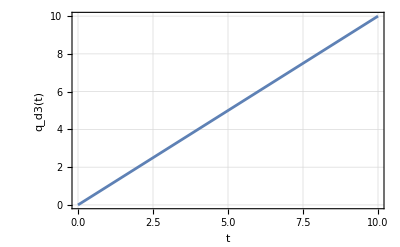

```mathematica
Plot[Subscript[q, d3][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d3(t)"},Frame->True,GridLines-> Automatic]
```

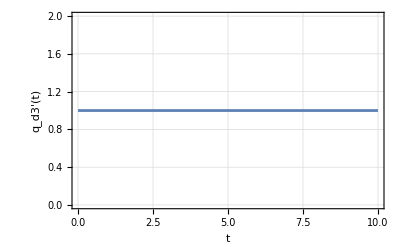

```mathematica
Plot[Subscript[q, d3]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d3'(t)"},Frame->True,GridLines-> Automatic]
```

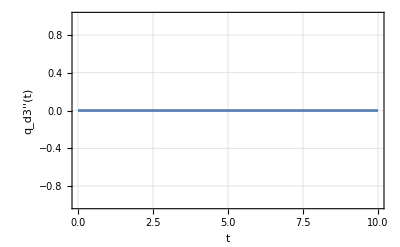

```mathematica
Plot[Subscript[q, d3]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d3''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_4 desired

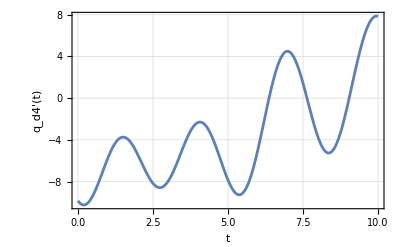

```mathematica
Plot[Subscript[q, d4]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d4'(t)"},Frame->True,GridLines-> Automatic]
```

q_d4[t] After Integration

```mathematica
Subscript[q, d4][t_]=Integrate[Subscript[q, d4]'[t],{t,0,t}]
```

-6.92115-1.46667 t+14.4656 Cos[(2 π t)/5] Sin[t]+4.34869 Sin[t] Sin[(π t)/5]+Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])

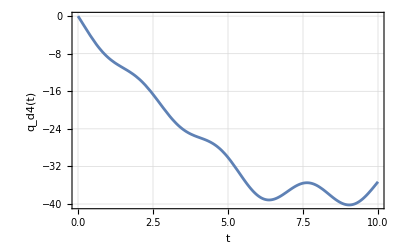

```mathematica
Plot[Subscript[q, d4][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d4(t)"},Frame->True,GridLines-> Automatic]
```

q_d4''[t] After Integration

```mathematica
Subscript[q, d4]''[t]
```

5.46472 Cos[t] Cos[(π t)/5]-37.3089 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-6.06548 Sin[t] Sin[(π t)/5]-Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-36.3561 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+28.7056 Sin[(2 π t)/5])

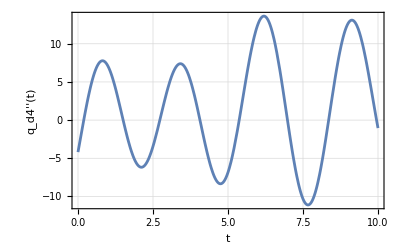

```mathematica
Plot[Subscript[q, d4]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d4''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_5 desired

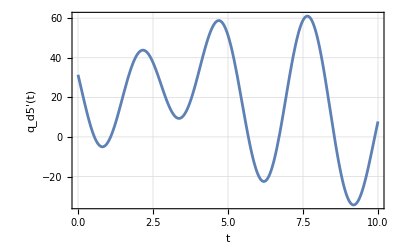

```mathematica
Plot[Subscript[q, d5]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d5'(t)"},Frame->True,GridLines-> Automatic]
```

q_d5[t] After Integration

```mathematica
Subscript[q, d5][t_]=Integrate[Subscript[q, d5]'[t],{t,0,t}]
```

108.492+51.9086 Cos[(π t)/5] Sin[t]+Cos[t] (-108.492 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-136.335 Sin[t] Sin[(2 π t)/5]

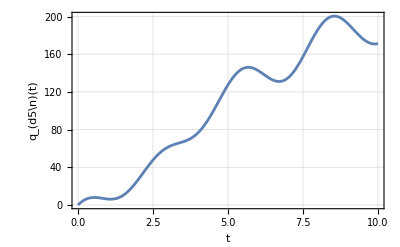

```mathematica
Plot[Subscript[q, d5][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_(d5\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d5''[t] After Integration

```mathematica
Subscript[q, d5]''[t]
```

-342.648 Cos[t] Cos[(2 π t)/5]-72.4013 Cos[(π t)/5] Sin[t]-Cos[t] (-108.492 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-65.2303 Cos[t] Sin[(π t)/5]+Cos[t] (171.324 Cos[(2 π t)/5]+12.8759 Sin[(π t)/5])+351.628 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-20.4927 Cos[(π t)/5]+136.335 Sin[(2 π t)/5])

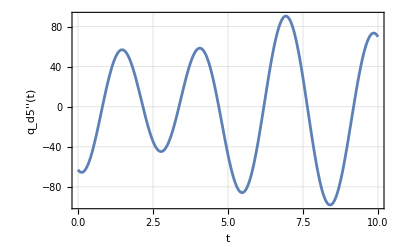

```mathematica
Plot[Subscript[q, d5]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d5''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_6 desired

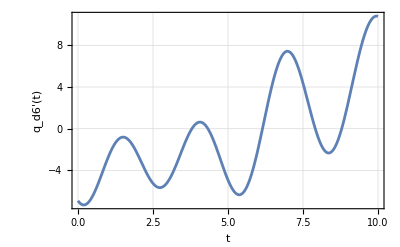

```mathematica
Plot[Subscript[q, d6]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d6'(t)"},Frame->True,GridLines-> Automatic]
```

q_6[t] After Integration

```mathematica
Subscript[q, d6][t_]=Integrate[Subscript[q, d6]'[t],{t,0,t}]
```

-6.92115+1.46667 t+14.4656 Cos[(2 π t)/5] Sin[t]+4.34869 Sin[t] Sin[(π t)/5]+Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])

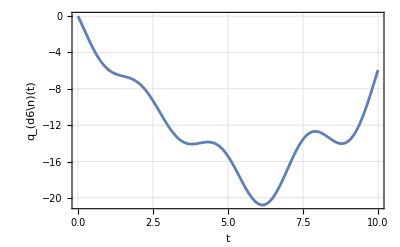

```mathematica
Plot[Subscript[q, d6][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_(d6\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d6''[t] After Integration

```mathematica
Subscript[q, d6]''[t]
```

5.46472 Cos[t] Cos[(π t)/5]-37.3089 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-6.06548 Sin[t] Sin[(π t)/5]-Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-36.3561 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+28.7056 Sin[(2 π t)/5])

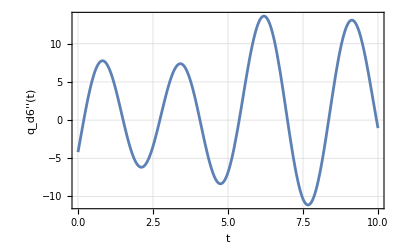

```mathematica
Plot[Subscript[q, d6]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d6''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_7 desired

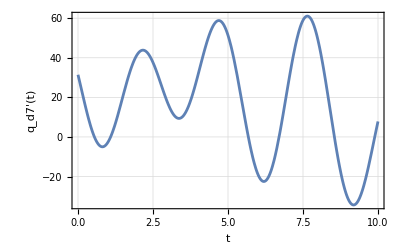

```mathematica
Plot[Subscript[q, d7]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d7'(t)"},Frame->True,GridLines-> Automatic]
```

q_d7[t] After Integration

```mathematica
Subscript[q, d7][t_]=Integrate[Subscript[q, d7]'[t],{t,0,t}]
```

108.492+51.9086 Cos[(π t)/5] Sin[t]+Cos[t] (-108.492 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-136.335 Sin[t] Sin[(2 π t)/5]

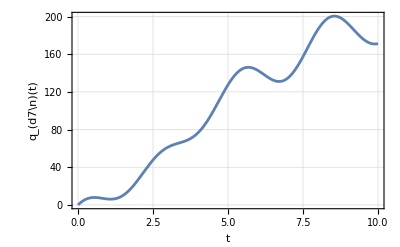

```mathematica
Plot[Subscript[q, d7][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_(d7\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_7''[t] After Integration

```mathematica
Subscript[q, d7]''[t]
```

-342.648 Cos[t] Cos[(2 π t)/5]-72.4013 Cos[(π t)/5] Sin[t]-Cos[t] (-108.492 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-65.2303 Cos[t] Sin[(π t)/5]+Cos[t] (171.324 Cos[(2 π t)/5]+12.8759 Sin[(π t)/5])+351.628 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-20.4927 Cos[(π t)/5]+136.335 Sin[(2 π t)/5])

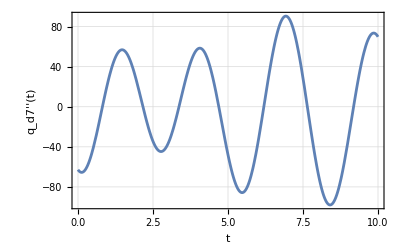

```mathematica
Plot[Subscript[q, d7]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d7''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_8 desired

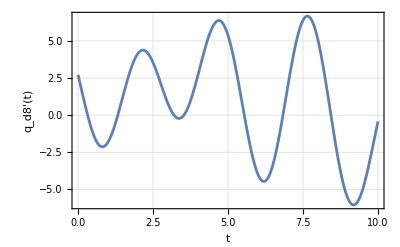

```mathematica
Plot[Subscript[q, d8]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d8'(t)"},Frame->True,GridLines-> Automatic]
```

q_8[t] After Integration

```mathematica
Subscript[q, d8][t_]=Integrate[Subscript[q, d8]'[t],{t,0,t}]
```

14.4656-1.46667 t+6.92115 Cos[(π t)/5] Sin[t]+Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]

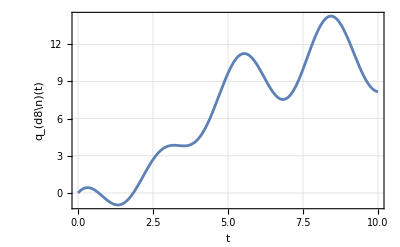

```mathematica
Plot[Subscript[q, d8][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_(d8\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_8''[t] After Integration

```mathematica
Subscript[q, d8]''[t]
```

-45.6864 Cos[t] Cos[(2 π t)/5]-9.65351 Cos[(π t)/5] Sin[t]-Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-8.69738 Cos[t] Sin[(π t)/5]+Cos[t] (22.8432 Cos[(2 π t)/5]+1.71679 Sin[(π t)/5])+46.8837 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])

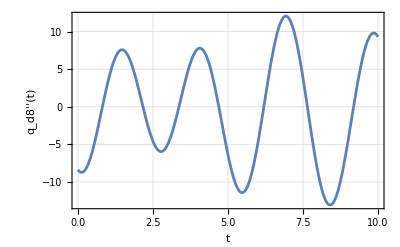

```mathematica
Plot[Subscript[q, d8]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d8''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_9 desired

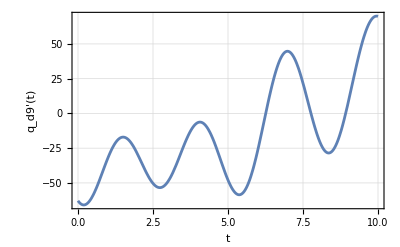

```mathematica
Plot[Subscript[q, d9]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9'(t)"},Frame->True,GridLines-> Automatic]
```

q_d9[t] After Integration

```mathematica
Subscript[q, d9][t_]=Integrate[Subscript[q, d9]'[t],{t,0,t}]
```

-51.9086+108.492 Cos[(2 π t)/5] Sin[t]+32.6152 Sin[t] Sin[(π t)/5]+Cos[t] (51.9086 Cos[(π t)/5]-136.335 Sin[(2 π t)/5])

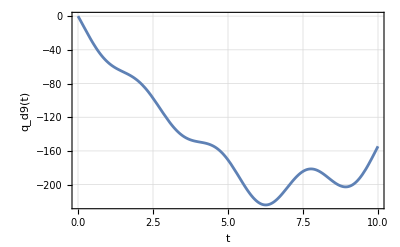

```mathematica
Plot[Subscript[q, d9][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9(t)"},Frame->True,GridLines-> Automatic]
```

q_d9''[t] After Integration

```mathematica
Subscript[q, d9]''[t]
```

40.9854 Cos[t] Cos[(π t)/5]-279.816 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-171.324 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-45.4911 Sin[t] Sin[(π t)/5]-Cos[t] (51.9086 Cos[(π t)/5]-136.335 Sin[(2 π t)/5])-272.671 Cos[t] Sin[(2 π t)/5]+Cos[t] (-20.4927 Cos[(π t)/5]+215.292 Sin[(2 π t)/5])

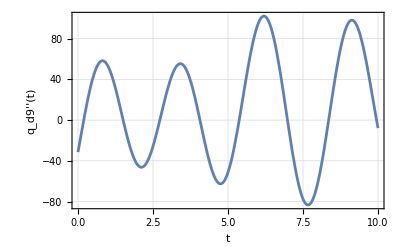

```mathematica
Plot[Subscript[q, d9]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_10 desired

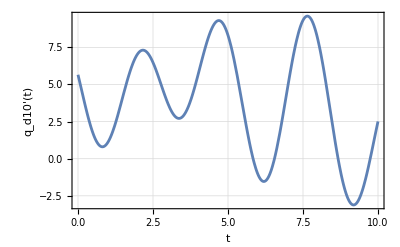

```mathematica
Plot[Subscript[q, d10]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d10'(t)"},Frame->True,GridLines-> Automatic]
```

q_d10[t] After Integration

```mathematica
Subscript[q, d10][t_]=Integrate[Subscript[q, d10]'[t],{t,0,t}]
```

14.4656+1.46667 t+6.92115 Cos[(π t)/5] Sin[t]+Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]

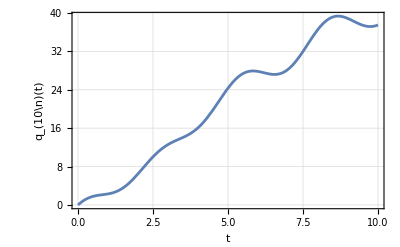

```mathematica
Plot[Subscript[q, d10][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_(10\n)(t)"},Frame->True,GridLines-> Automatic]
```

q_d10''[t] After Integration

```mathematica
Subscript[q, d10]''[t]
```

-45.6864 Cos[t] Cos[(2 π t)/5]-9.65351 Cos[(π t)/5] Sin[t]-Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-8.69738 Cos[t] Sin[(π t)/5]+Cos[t] (22.8432 Cos[(2 π t)/5]+1.71679 Sin[(π t)/5])+46.8837 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])

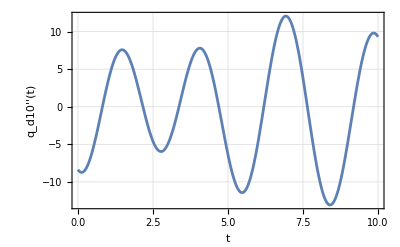

```mathematica
Plot[Subscript[q, d10]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d10''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_11 desired

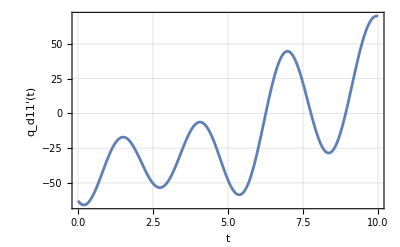

```mathematica
Plot[Subscript[q, d11]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d11'(t)"},Frame->True,GridLines-> Automatic]
```

q_d11[t] After Integration

```mathematica
Subscript[q, d11][t_]=Integrate[Subscript[q, d11]'[t],{t,0,t}]
```

-51.9086+108.492 Cos[(2 π t)/5] Sin[t]+32.6152 Sin[t] Sin[(π t)/5]+Cos[t] (51.9086 Cos[(π t)/5]-136.335 Sin[(2 π t)/5])

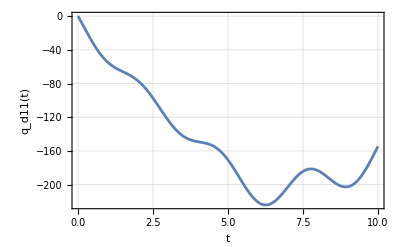

```mathematica
Plot[Subscript[q, d11][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d11(t)"},Frame->True,GridLines-> Automatic]
```

q_d11''[t] After Integration

```mathematica
Subscript[q, d11]''[t]
```

40.9854 Cos[t] Cos[(π t)/5]-279.816 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-171.324 Cos[(2 π t)/5]-32.6152 Sin[(π t)/5])-45.4911 Sin[t] Sin[(π t)/5]-Cos[t] (51.9086 Cos[(π t)/5]-136.335 Sin[(2 π t)/5])-272.671 Cos[t] Sin[(2 π t)/5]+Cos[t] (-20.4927 Cos[(π t)/5]+215.292 Sin[(2 π t)/5])

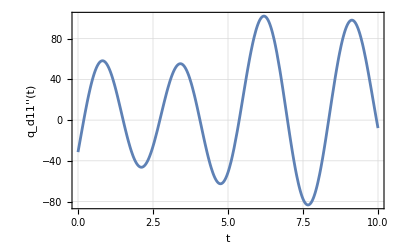

```mathematica
Plot[Subscript[q, d11]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d11''(t)"},Frame->True,GridLines-> Automatic]
```

#### Path Planned Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
Subscript[q, 1][t_]=Subscript[q, d1][t];
Subscript[q, 2][t_]=Subscript[q, d2][t];
Subscript[q, 3][t_]=Subscript[q, d3][t];
Subscript[q, 4][t_]=Subscript[q, d4][t];
Subscript[q, 5][t_]=Subscript[q, d5][t];
Subscript[q, 6][t_]=Subscript[q, d6][t];
Subscript[q, 7][t_]=Subscript[q, d7][t];
Subscript[q, 8][t_]=Subscript[q, d8][t];
Subscript[q, 9][t_]=Subscript[q, d9][t];
Subscript[q, 10][t_]=Subscript[q, d10][t];
Subscript[q, 11][t_]=Subscript[q, d11][t];
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-6,50},{-6,50},{-6,50}},AspectRatio->1,AxesLabel->{"q_d1","q_d2","q_z"}]
```

-Graphics3D-

```mathematica
robotGraphicPathKinAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicPathKinAnimT[t_]=robotGraphicPathKinAnim;
```

Loop over time

```mathematica
(*{-0.15scale,scale},{-0.15scale,0.15scale},{-scale,scale}*)
```

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathKinAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-6,50},{-6,50},{-6,50}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Subscript[T, man],delT},AnimationRunning->False]
```

## Path planned dynamic simulation

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
ω=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
Subscript[T, mot][1]=.  
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
Subscript[q, 4]''[t_]=.;
Subscript[q, 4]'[t_]=.;
Subscript[q, 5]''[t_]=.;
Subscript[q, 5]'[t_]=.;
Subscript[q, 6]''[t_]=.;
Subscript[q, 6]'[t_]=.;
Subscript[q, 7]''[t_]=.;
Subscript[q, 7]'[t_]=.;
Subscript[q, 8]''[t_]=.;
Subscript[q, 8]'[t_]=.;
Subscript[q, 9]''[t_]=.;
Subscript[q, 9]'[t_]=.;
Subscript[q, 10]''[t_]=.;
Subscript[q, 10]'[t_]=.;
Subscript[q, 11]''[t_]=.;
Subscript[q, 11]'[t_]=.;
```

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

Unset::norep: Assignment on Subscript for T_mot[1] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[2] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[3] not found.

$Failed

Unset::norep: Assignment on Subscript for T_mot[4] not found.

$Failed

Unset::norep: Assignment on Derivative for q_4''[t_] not found.

Unset::norep: Assignment on Derivative for q_4'[t_] not found.

Unset::norep: Assignment on Derivative for q_5''[t_] not found.

Unset::norep: Assignment on Derivative for q_5'[t_] not found.

Unset::norep: Assignment on Derivative for q_6''[t_] not found.

Unset::norep: Assignment on Derivative for q_6'[t_] not found.

Unset::norep: Assignment on Derivative for q_7''[t_] not found.

Unset::norep: Assignment on Derivative for q_7'[t_] not found.

Unset::norep: Assignment on Derivative for q_8''[t_] not found.

Unset::norep: Assignment on Derivative for q_8'[t_] not found.

Unset::norep: Assignment on Derivative for q_9''[t_] not found.

Unset::norep: Assignment on Derivative for q_9'[t_] not found.

Unset::norep: Assignment on Derivative for q_10''[t_] not found.

Unset::norep: Assignment on Derivative for q_10'[t_] not found.

Unset::norep: Assignment on Derivative for q_11''[t_] not found.

Unset::norep: Assignment on Derivative for q_11'[t_] not found.

#### Now we see how the robot works under control following the chosen path.

Assign control gains found above.  Take note that these may be unreasonably high and must be factor into any overall design...can the amplifiers/motors needed be reasonably built.  If not trade-offs on size and speed are needed.

```mathematica
For[i=1,i≤ Subscript[N, dof],i++,Subscript[K, prop][i]=Subscript[K, prop][i]/.solGains[i]/.tConstRules[i];Subscript[K, Int][i]=Subscript[K, Int][i]/.solGains[i]/.tConstRules[i];Subscript[K, deriv][i]=Subscript[K, deriv][i]/.solGains[i]/.tConstRules[i];Print["K_prop[",i,"]=",Subscript[K, prop][i],", K_Int[",i,"]=",Subscript[K, Int][i],", K_deriv[",i,"]=",Subscript[K, deriv][i]]]
```

K_prop[1]=1426.79, K_Int[1]=17378.6, K_deriv[1]=90.8426

K_prop[2]=1423.97, K_Int[2]=17344.3, K_deriv[2]=90.663

K_prop[3]=1498.26, K_Int[3]=18249.1, K_deriv[3]=95.3929

K_prop[4]=1498.26, K_Int[4]=18249.1, K_deriv[4]=95.3929

Simulate the system with the planned path.  This may take a while.

```mathematica
(*"EquationSimplification"->"Residual",{"IndexReduction"->Automatic}}*Method->{"EquationSimplification"->"Residual"}*)
```

#### Equations IKM

```mathematica
eq1n=eqin5//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t]}
Cases[eq1n,q__[t],Infinity]//Union
```

u_1[t]==R (Cos[q_3[t]] (0.5 ω_1[t]+0.5 ω_2[t])+Sin[q_3[t]] (0.5 ω_3[t]+0.5 ω_4[t]))

{q_3[t],u_1[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t]}

```mathematica
eq2n=eqin6//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t]}
Cases[eq2n,q__[t],Infinity]//Union
```

u_2[t]==R (Sin[q_3[t]] (0.5 ω_1[t]+0.5 ω_2[t])+Cos[q_3[t]] (-0.5 ω_3[t]-0.5 ω_4[t]))

{q_3[t],u_2[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t]}

```mathematica
eq3n=eqin7//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t]}
Cases[eq3n,q__[t],Infinity]//Union
```

Ω[t]==R (-0.0568182 ω_1[t]+0.0568182 ω_2[t]-0.0568182 ω_3[t]+0.0568182 ω_4[t])

{Ω[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t]}

```mathematica
(*eq4n=eqQ5//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t],Subscript[Q, 5]'[t]-> Subscript[q, 5]'[t],Subscript[Q, 7]'[t]-> Subscript[q, 7]'[t],Subscript[Q, 9]'[t]-> Subscript[q, 9]'[t],Subscript[Q, 11]'[t]-> Subscript[q, 11]'[t]}
Cases[eq4n,q__[t],Infinity]//Union*)
```

```mathematica
eq5n=eqQ5//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t],Subscript[Q, 5]'[t]-> Subscript[q, 5]'[t],Subscript[Q, 7]'[t]-> Subscript[q, 7]'[t],Subscript[Q, 9]'[t]-> Subscript[q, 9]'[t],Subscript[Q, 11]'[t]-> Subscript[q, 11]'[t]}
Cases[eq5n,q__[t],Infinity]//Union
```

q_5'[t]==(Sin[q_3[t]] u_1[t]-Cos[q_3[t]] u_2[t])/r

{q_3[t],u_1[t],u_2[t],q_5'[t]}

```mathematica
eq6n=eqQ7//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t],Subscript[Q, 5]'[t]-> Subscript[q, 5]'[t],Subscript[Q, 7]'[t]-> Subscript[q, 7]'[t],Subscript[Q, 9]'[t]-> Subscript[q, 9]'[t],Subscript[Q, 11]'[t]-> Subscript[q, 11]'[t]}
Cases[eq6n,q__[t],Infinity]//Union
```

q_7'[t]==(Sin[q_3[t]] u_1[t]-Cos[q_3[t]] u_2[t])/r

{q_3[t],u_1[t],u_2[t],q_7'[t]}

```mathematica
eq7n=eqQ9//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t],Subscript[Q, 5]'[t]-> Subscript[q, 5]'[t],Subscript[Q, 7]'[t]-> Subscript[q, 7]'[t],Subscript[Q, 9]'[t]-> Subscript[q, 9]'[t],Subscript[Q, 11]'[t]-> Subscript[q, 11]'[t]}
Cases[eq7n,q__[t],Infinity]//Union
```

q_9'[t]==(Cos[q_3[t]] u_1[t]+Sin[q_3[t]] u_2[t])/r

{q_3[t],u_1[t],u_2[t],q_9'[t]}

```mathematica
eq8n=eqQ11//.{Subscript[Q, 1]'[t]-> Subscript[u, 1][t],Subscript[Q, 2]'[t]-> Subscript[u, 2][t],Subscript[Q, 3]'[t]->  Ω[t],Subscript[Q, 4]'[t]-> Subscript[ω, 1][t],Subscript[Q, 6]'[t]-> Subscript[ω, 2][t],Subscript[Q, 8]'[t]-> Subscript[ω, 3][t],Subscript[Q, 10]'[t]-> Subscript[ω, 4][t],Subscript[Q, 1][t]-> Subscript[q, 1][t],Subscript[Q, 2][t]-> Subscript[q, 2][t],Subscript[Q, 3][t]-> Subscript[q, 3][t],Subscript[Q, 4][t]-> Subscript[q, 4][t],Subscript[Q, 5][t]-> Subscript[q, 5][t],Subscript[Q, 6][t]-> Subscript[q, 6][t],Subscript[Q, 7][t]-> Subscript[q, 7][t],Subscript[Q, 8][t]-> Subscript[q, 8][t],Subscript[Q, 9][t]-> Subscript[q, 9][t],Subscript[Q, 10][t]-> Subscript[q, 10][t],Subscript[Q, 11][t]-> Subscript[q, 11][t],Subscript[Q, 5]'[t]-> Subscript[q, 5]'[t],Subscript[Q, 7]'[t]-> Subscript[q, 7]'[t],Subscript[Q, 9]'[t]-> Subscript[q, 9]'[t],Subscript[Q, 11]'[t]-> Subscript[q, 11]'[t]}
Cases[eq8n,q__[t],Infinity]//Union
```

q_11'[t]==(Cos[q_3[t]] u_1[t]+Sin[q_3[t]] u_2[t])/r

{q_3[t],u_1[t],u_2[t],q_11'[t]}

```mathematica
eqCn[1]=eqC[1]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqCn[1],q__[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],Tm_1[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
eqCn[2]=eqC[2]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqCn[2],q__[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],Tm_2[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
eqCn[3]=eqC[3]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqCn[3],q__[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],Tm_3[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
eqCn[4]=eqC[4]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqCn[4],q__[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],Tm_4[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
eqMn[1]=eqM[1]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqMn[1],q__[t],Infinity]//Union
```

-17378.6 (-6.92115-1.46667 t+14.4656 Cos[(2 π t)/5] Sin[t]+4.34869 Sin[t] Sin[(π t)/5]+Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-q_4[t])-1426.79 (-1.46667+14.4656 Cos[t] Cos[(2 π t)/5]+2.73236 Cos[(π t)/5] Sin[t]+Cos[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])+4.34869 Cos[t] Sin[(π t)/5]-Sin[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]-ω_1[t])+Tm_1'[t]-90.8426 (5.46472 Cos[t] Cos[(π t)/5]-37.3089 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-6.06548 Sin[t] Sin[(π t)/5]-Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-36.3561 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+28.7056 Sin[(2 π t)/5])-ω_1'[t])

{Cos[t],Sin[t],q_4[t],ω_1[t],Tm_1'[t],ω_1'[t]}

```mathematica
eqMn[2]=eqM[2]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqMn[2],q__[t],Infinity]//Union
```

-17344.3 (-6.92115+1.46667 t+14.4656 Cos[(2 π t)/5] Sin[t]+4.34869 Sin[t] Sin[(π t)/5]+Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-q_6[t])-1423.97 (1.46667+14.4656 Cos[t] Cos[(2 π t)/5]+2.73236 Cos[(π t)/5] Sin[t]+Cos[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])+4.34869 Cos[t] Sin[(π t)/5]-Sin[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]-ω_2[t])+Tm_2'[t]-90.663 (5.46472 Cos[t] Cos[(π t)/5]-37.3089 Cos[(2 π t)/5] Sin[t]-2 Sin[t] (-22.8432 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-6.06548 Sin[t] Sin[(π t)/5]-Cos[t] (6.92115 Cos[(π t)/5]-18.1781 Sin[(2 π t)/5])-36.3561 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+28.7056 Sin[(2 π t)/5])-ω_2'[t])

{Cos[t],Sin[t],q_6[t],ω_2[t],Tm_2'[t],ω_2'[t]}

```mathematica
eqMn[3]=eqM[3]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqMn[3],q__[t],Infinity]//Union
```

-18249.1 (14.4656-1.46667 t+6.92115 Cos[(π t)/5] Sin[t]+Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]-q_8[t])-1498.26 (-1.46667+6.92115 Cos[t] Cos[(π t)/5]-22.8432 Cos[(2 π t)/5] Sin[t]-Sin[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-4.34869 Sin[t] Sin[(π t)/5]-18.1781 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])-ω_3[t])+Tm_3'[t]-95.3929 (-45.6864 Cos[t] Cos[(2 π t)/5]-9.65351 Cos[(π t)/5] Sin[t]-Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-8.69738 Cos[t] Sin[(π t)/5]+Cos[t] (22.8432 Cos[(2 π t)/5]+1.71679 Sin[(π t)/5])+46.8837 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])-ω_3'[t])

{Cos[t],Sin[t],q_8[t],ω_3[t],Tm_3'[t],ω_3'[t]}

```mathematica
eqMn[4]=eqM[4]//.{Subscript[q, 1]'[t]-> Subscript[u, 1][t],Subscript[q, 2]'[t]-> Subscript[u, 2][t],Subscript[q, 3]'[t]-> Ω[t],Subscript[q, 4]'[t]-> Subscript[ω, 1][t],Subscript[q, 6]'[t]-> Subscript[ω, 2][t],Subscript[q, 8]'[t]-> Subscript[ω, 3][t],Subscript[q, 10]'[t]-> Subscript[ω, 4][t],Subscript[q, 4]''[t]-> Subscript[ω, 1]'[t],Subscript[q, 6]''[t]-> Subscript[ω, 2]'[t],Subscript[q, 8]''[t]-> Subscript[ω, 3]'[t],Subscript[q, 10]''[t]-> Subscript[ω, 4]'[t]}
Cases[eqMn[4],q__[t],Infinity]//Union
```

-18249.1 (14.4656+1.46667 t+6.92115 Cos[(π t)/5] Sin[t]+Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-18.1781 Sin[t] Sin[(2 π t)/5]-q_10[t])-1498.26 (1.46667+6.92115 Cos[t] Cos[(π t)/5]-22.8432 Cos[(2 π t)/5] Sin[t]-Sin[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-4.34869 Sin[t] Sin[(π t)/5]-18.1781 Cos[t] Sin[(2 π t)/5]+Cos[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])-ω_4[t])+Tm_4'[t]-95.3929 (-45.6864 Cos[t] Cos[(2 π t)/5]-9.65351 Cos[(π t)/5] Sin[t]-Cos[t] (-14.4656 Cos[(2 π t)/5]-4.34869 Sin[(π t)/5])-8.69738 Cos[t] Sin[(π t)/5]+Cos[t] (22.8432 Cos[(2 π t)/5]+1.71679 Sin[(π t)/5])+46.8837 Sin[t] Sin[(2 π t)/5]-2 Sin[t] (-2.73236 Cos[(π t)/5]+18.1781 Sin[(2 π t)/5])-ω_4'[t])

{Cos[t],Sin[t],q_10[t],ω_4[t],Tm_4'[t],ω_4'[t]}

```mathematica
EQN1=Subscript[u, 1][t]==Subscript[q, 1]'[t]
```

u_1[t]==q_1'[t]

```mathematica
EQN2=Subscript[u, 2][t]==Subscript[q, 2]'[t]
```

u_2[t]==q_2'[t]

```mathematica
EQN3=Ω[t]==Subscript[q, 3]'[t]
```

Ω[t]==q_3'[t]

```mathematica
EQN4=Subscript[ω, 1][t]==Subscript[q, 4]'[t]
```

ω_1[t]==q_4'[t]

```mathematica
EQN5=Subscript[ω, 2][t]==Subscript[q, 6]'[t]
```

ω_2[t]==q_6'[t]

```mathematica
EQN6=Subscript[ω, 3][t]==Subscript[q, 8]'[t]
```

ω_3[t]==q_8'[t]

```mathematica
EQN7=Subscript[ω, 4][t]==Subscript[q, 10]'[t]
```

ω_4[t]==q_10'[t]

#### After making equations first order(working)

```mathematica
R=3;
r=0.4;
Subscript[t, 0]=0;
Subscript[t, f]=Subscript[T, man];
g=32.17(12);solPathDyn=Monitor[NDSolve[{EQN1,EQN2,EQN3,EQN4,EQN5,EQN6,EQN7,eq1n,eq2n,eq3n(*,eq4n*),eq5n,eq6n,eq7n,eq8n, eqCn[1]==0,eqCn[2]==0,eqCn[3]==0,eqCn[4]==0,eqMn[1]==0,eqMn[2]==0,eqMn[3]==0,eqMn[4]==0,Subscript[q, 1][0]==Subscript[q, d1][0],Subscript[u, 1][0]==Subscript[q, d1]'[0],Subscript[q, 2][0]==Subscript[q, d2][0],Subscript[u, 2][0]==Subscript[q, d2]'[0],Subscript[q, 3][0]==Subscript[q, d3][0],Ω[0]==Subscript[q, d3]'[0],Subscript[ω, 1][0]==Subscript[q, d4]'[0],Subscript[q, 4][0]==Subscript[q, d4][0],Subscript[q, 5][0]==Subscript[q, d5][0],Subscript[ω, 2][0]==Subscript[q, d6]'[0],Subscript[q, 6][0]==Subscript[q, d6][0],Subscript[q, 7][0]==Subscript[q, d7][0],Subscript[ω, 3][0]==Subscript[q, d8]'[0],Subscript[q, 8]'[0]==Subscript[q, d8]'[0],Subscript[q, 8][0]==Subscript[q, d8][0],Subscript[q, 9][0]==Subscript[q, d9][0],Subscript[ω, 4][0]==Subscript[q, d10]'[0],Subscript[q, 10][0]==Subscript[q, d10][0],Subscript[q, 11][0]==Subscript[q, d11][0],Subscript[Tm, 1][0]==0,Subscript[Tm, 2][0]==0,Subscript[Tm, 3][0]==0,Subscript[Tm, 4][0]==0},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11],Subscript[Tm, 1],Subscript[Tm, 2],Subscript[Tm, 3],Subscript[Tm, 4],Subscript[u, 1], Subscript[u, 2],Ω, Subscript[ω, 1], Subscript[ω, 2], Subscript[ω, 3], Subscript[ω, 4]},{t,Subscript[t, 0],Subscript[t, f]},StepMonitor:>(time=t;)(*,WorkingPrecision -> 4 *), MaxSteps->5000,Method-> {"EquationSimplification"-> "Residual"(*,{"IndexReduction"-> Automatic}*)}],ProgressIndicator[time,{Subscript[t, 0],Subscript[t, f]}]]//First
```

{q_1→InterpolatingFunction[…],q_2→InterpolatingFunction[…],q_3→InterpolatingFunction[…],q_4→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…],q_11→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…],u_1→InterpolatingFunction[…],u_2→InterpolatingFunction[…],Ω→InterpolatingFunction[…],ω_1→InterpolatingFunction[…],ω_2→InterpolatingFunction[…],ω_3→InterpolatingFunction[…],ω_4→InterpolatingFunction[…]}

#### q_4 and motor force plots

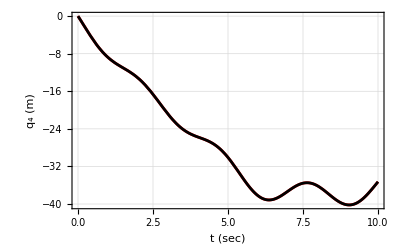

```mathematica
Plot[{Subscript[q, d4][t],Subscript[q, 4][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_4 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

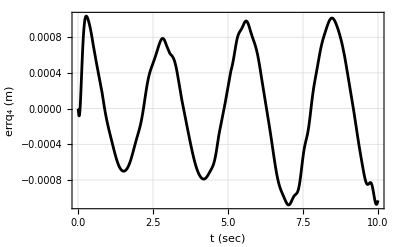

```mathematica
Plot[(Subscript[q, d4][t]-Subscript[q, 4][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_4 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

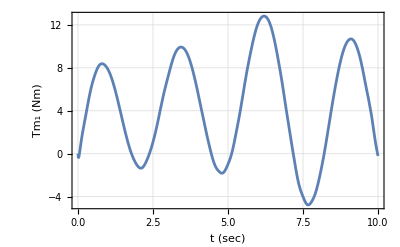

```mathematica
Plot[Subscript[Tm, 1][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (Nm)"},PlotRange->All]
```

#### q_6 and motor force plots

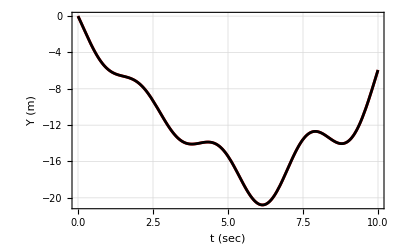

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

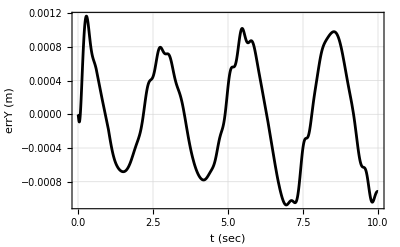

```mathematica
Plot[Subscript[q, d6][t]-Subscript[q, 6][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errY (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

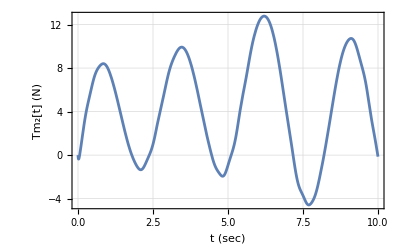

```mathematica
Plot[Subscript[Tm, 2][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2[t] (N)"},PlotRange->All]
```

#### q_8 and motor torque plots

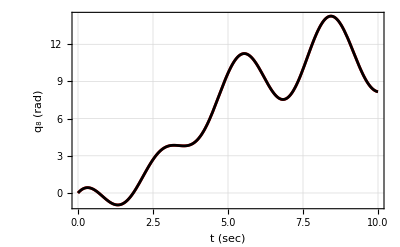

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

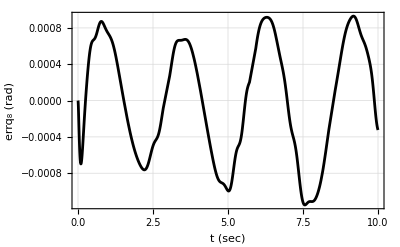

```mathematica
Plot[(Subscript[q, d8][t]-Subscript[q, 8][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

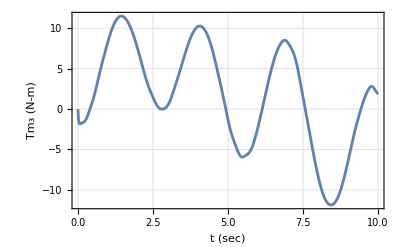

```mathematica
Plot[Subscript[Tm, 3][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"},PlotRange->All]
```

#### q_10 and motor torque plots

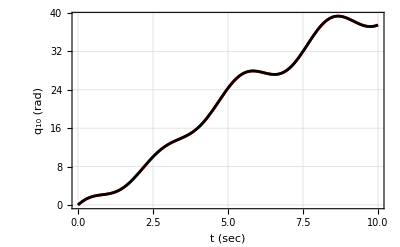

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

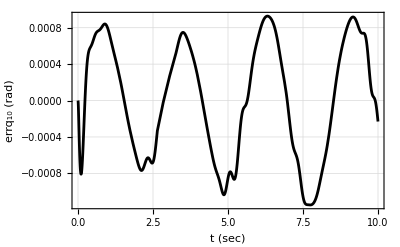

```mathematica
Plot[(Subscript[q, d10][t]-Subscript[q, 10][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

```mathematica
Plot[Subscript[Tm, 3][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"},PlotRange->All]
```

-Graphics-

#### q_1

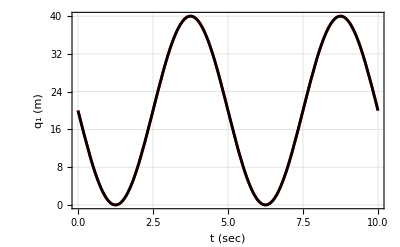

```mathematica
Plot[{Subscript[q, d1][t],Subscript[q, 1][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_1 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

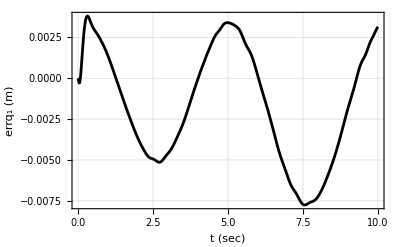

```mathematica
Plot[(Subscript[q, d1][t]-Subscript[q, 1][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_1 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_2

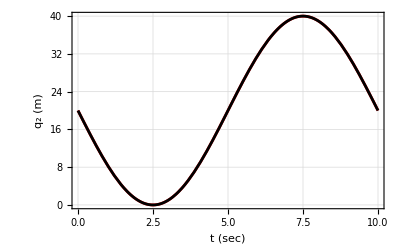

```mathematica
Plot[{Subscript[q, d2][t],Subscript[q, 2][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_2 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

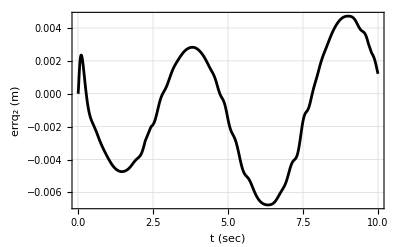

```mathematica
Plot[(Subscript[q, d2][t]-Subscript[q, 2][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_2 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_3

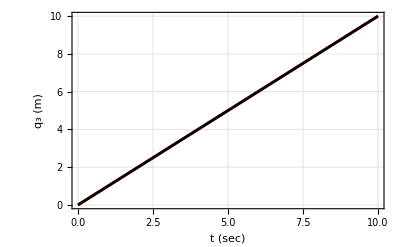

```mathematica
Plot[{Subscript[q, d3][t],Subscript[q, 3][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_3 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

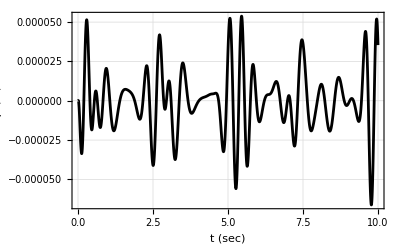

```mathematica
Plot[(Subscript[q, d3][t]-Subscript[q, 3][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_3 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_5

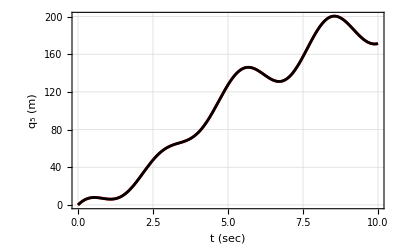

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

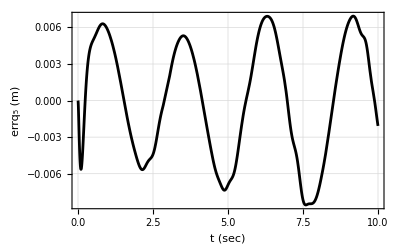

```mathematica
Plot[(Subscript[q, d5][t]-Subscript[q, 5][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_5 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_7

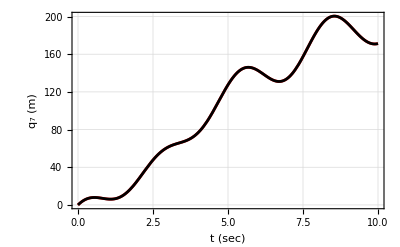

```mathematica
Plot[{Subscript[q, d7][t],Subscript[q, 7][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_7 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

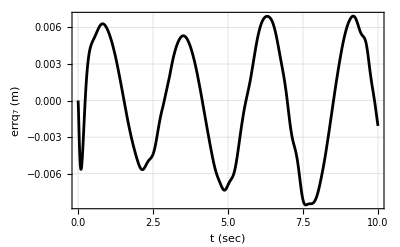

```mathematica
Plot[(Subscript[q, d7][t]-Subscript[q, 7][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_7 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_9

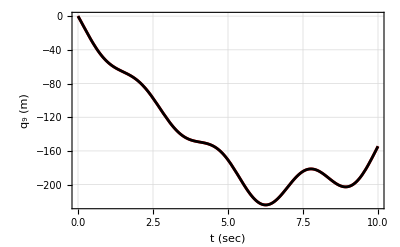

```mathematica
Plot[{Subscript[q, d9][t],Subscript[q, 9][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_9 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

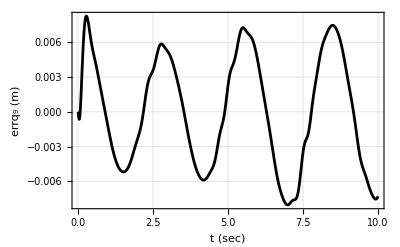

```mathematica
Plot[(Subscript[q, d9][t]-Subscript[q, 9][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_9 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### q_11

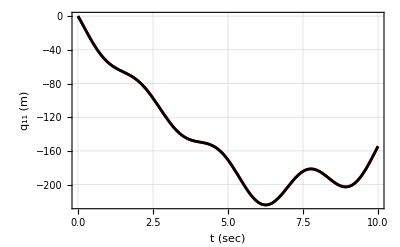

```mathematica
Plot[{Subscript[q, d11][t],Subscript[q, 11][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_11 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

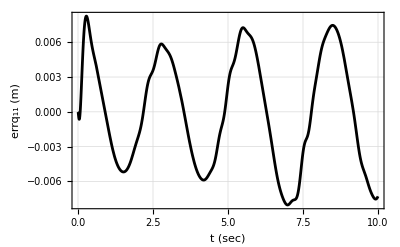

```mathematica
Plot[(Subscript[q, d11][t]-Subscript[q, 11][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_11 (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

#### Animation of the path planned motion

```mathematica
Subscript[q, 1][t_]=Subscript[q, 1][t]/.solPathDyn;
Subscript[q, 2][t_]=Subscript[q, 2][t]/.solPathDyn;
Subscript[q, 3][t_]=Subscript[q, 3][t]/.solPathDyn;
Subscript[q, 4][t_]=Subscript[q, 4][t]/.solPathDyn;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solPathDyn;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solPathDyn;
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solPathDyn;
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solPathDyn;
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solPathDyn;
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solPathDyn;
Subscript[q, 11][t_]=Subscript[q, 11][t]/.solPathDyn;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
scale=40;
pathPlot=ParametricPlot3D[{Subscript[q, d1][t],Subscript[q, d2][t],Subscript[q, z][t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-0.5scale,scale},{-0.5scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"q_d1'[t]","q_d2'[t]","q_d3'[t]"}]
```

-Graphics3D-

```mathematica
robotGraphicPathDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicPathDynAnimT[t_]=robotGraphicPathDynAnim;
```

Loop over time

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Subscript[T, man],delT},AnimationRunning->False]
```

```mathematica
Animate[Show[Graphics3D[robotGraphicPathDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Subscript[T, man],delT},AnimationRunning->False]
```